# Regulatory and Signaling pathways

## A computational study towards understanding models of molecular networks

Emma Hokken 10572090
Natasja Wezel 11027649

## Complex biomolecular systems can often not be reduced to elementary properties of individual components. Mathematical models that can explain and predict cellular functions are very useful to understand and engineer them. Two of the main methods used today to model molecular and gene networks are: continuous (quantitative) and discrete (qualitative) modelling.

## Analysing mathematical models of signal-response systems Quantitative chemical kinetic models

Biochemical and cellular processes follow chemical and physical laws. If underlying chemical processes are known, the basis of thermodynamical and chemical kinetics can describe the behaviour of a system. Applying system theory to chemical kinetics is the most common approach to model molecular networks. Chemical kinetics uses the notion of processes where reactants are consumed and products are generated.

The rate at which these processes take place is dependent on the quantity of the components involved, reaction order and parameters. The mathematical expressions depend on the assumptions that are made.

-Graphics-
Figure 1. Some simple networks with different dynamic behaviors. S = Signal strength (e.g. concentration of mRNA), R = Response Element (e.g. protein concentration), E = Enzyme, EP = Phosphorylated Enzyme. A) Perfect Adaptation. B-D) Other simple networks, with other types of feedback.

Figure 1a shows a network for perfect adaption. This behaviour is typical of chemotactic systems that respond to an abrupt change in attractants or repellents and then adapt to a constant level of signal.
The kinetic equations for a system with perfect adaption are derived using the law of mass action:
ⅆR/ⅆt=k_1 S-k_2 X R,     with k_1=k_2=2,k_3=k_4=1
ⅆX/ⅆt=k_3 S-k_4 X

For three other types of feedback, different kinetic equations are defined.
Negative feedback: Homeostasis

	ⅆR/ⅆt=k_0 E(R)-k_2 S R
E(R)=G(k_3,k_4 R,J_3,J_4)  	with k_0 = 1, k_2= 1, k_3= 0.5, k_4= 1, J_3= J_4= 0.01. 
	
Positive Feedback: Mutual inhibition

	ⅆR/ⅆt=k_0+k_1 S-k_2 R-k'_2 E(R) R
E(R)=G(k_3,k_4 R,J_3,J_4)		with k_0 = 0, k_1= 1, k_2= 0.05, k'_2= 0.5, k_3= 1, k_4= 0.2, J_3= J_4= 0.05.

Positive Feedback Mutual activation

	ⅆR/ⅆt=k_0 E_p(R)+k_1 S-k_2 R
E_p(R)=G(k_3 R,k_4,J_3,J_4)	with k_0 = 0.4, k_1= 0.01, k_2= k_3= 1, k_4= 0.2, J_3= J_4= 0.05.

G refers to the Goldbeter-Koshland function and is defined as: 
	G(u,v,J,K)=(2u K)/(v-u+v J+u K+√((v - u + v J + u K)^2- 4(v-u)u K))

Methods
We look at the different dynamic behaviors that the different simple networks in figure 1 express. To look at the dynamics of the systems, we need to solve them assuming steady-state. For each of the networks (1b-d) we will first plot the reaction rate as a function of R and a constant S. Then we will look at signal-response curves.

For Homeostasis we take S = 0.5, 1.0 and 1.5
For Mutual Inhibition we take S = 1.0, 1.5 and 2.0

Results and Discussion

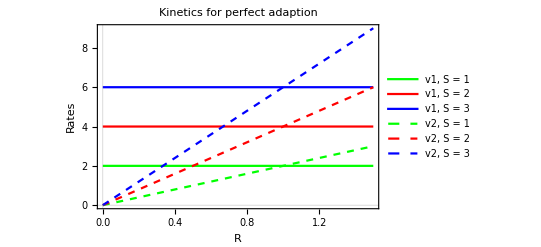

```mathematica
paramsA={k1->2,k2->2,k3->1,k4->1};
rateqsA={v1->k1*s,v2->k2*k3*s*r/k4};

(*Plot rates as a function of R at constant S*)
Plot[{v1/.rateqsA/.paramsA/.s->1,v1/.rateqsA/.paramsA/.s->2,v1/.rateqsA/.paramsA/.s->3,v2/.rateqsA/.paramsA/.s->1,v2/.rateqsA/.paramsA/.s->2,v2/.rateqsA/.paramsA/.s->3},{r,0,1.5},
Frame->True,
FrameLabel->{"R","Rates"},PlotLegends->{"v1, S = 1","v1, S = 2","v1, S = 3","v2, S = 1", "v2, S = 2" , "v2, S = 3"},PlotLabel->Style["Kinetics for perfect adaption",FontSize->18],
PlotTheme->"Scientific",
PlotStyle-> {Green, Red, Blue, {Dashed, Green}, {Dashed, Red}, {Dashed, Blue}}]
```

We see here that .........???????????

Next, the concentrations of all the species over time is plotted. S is defined in incremental steps with values S = 0, 1, 2, 3 and 4, each step lasting t = 4.

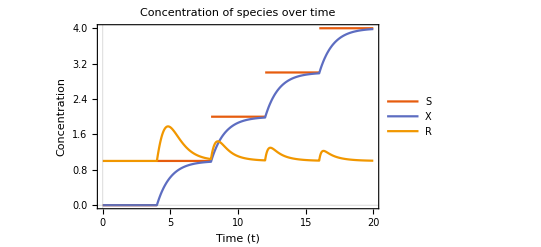

```mathematica
solT[t_] = NDSolve[{r'[t] == 2*Floor[t/4] - 2 * x[t] * r[t], x'[t] == 1* Floor[t/4] - 1*x[t], r[0] == 1, x[0]== 0}, {r[t], x[t]}, {t,0,20}];
 
Plot[{Floor[t/4], Evaluate[{x[t]/. solT[t], r[t] /. solT[t]}]},{t,0,20},  
PlotLegends->{"S", "X", "R"},
Frame-> True,
FrameLabel-> {"Time (t)", "Concentration"},
PlotTheme->"Scientific",
PlotLabel-> Style["Concentration of species over time", FontSize->18]]
```

Here, we see the evolution of each species in time. We see that the Signal gets higher every 4 time steps, as we defined it too. The Response, R, increases each time, and goes back to its equilibrium, a concentration of 1. Finally, we see that the concentration of X keeps increasing, as we would expect in a feed-forward control loop.

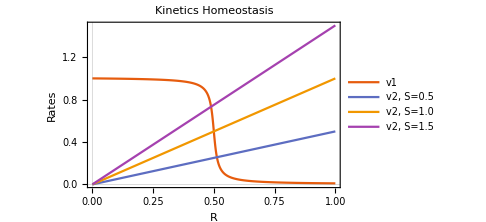

```mathematica
Remove[k0,k1,k2,k3,k4,J3,J4,s,r]

G[u_,v_,J_,K_]=2*u*K/(v-u+v*J+u*K+((v-u+v*J+u*K)^2-4*(v-u)*u*K)^0.5);

paramsHomeo={k0->1,k2->1,k3->0.5,k4->1,J3->0.01,J4->0.01};
equationsA={v1->k0*G[k3,k4*r,J3,J4], v2-> k2*s*r};

homeostasisKinetics = Plot[{v1/.equationsA/.paramsHomeo,
v2/.equationsA/.paramsHomeo/.s->0.5,v2/.equationsA/.paramsHomeo/.s->1,v2/.equationsA/.paramsHomeo/.s->1.5},
{r,0,1},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"R","Rates"}, 
PlotLabel-> Style["Kinetics Homeostasis", FontSize-> 18],
PlotLegends->{"v1","v2, S=0.5", "v2, S=1.0","v2, S=1.5"},
ImageSize->Medium]

solHomeo = Solve[0 == (v1-v2) /. equationsA,r];
homeostasisSignalResponse =Plot[r/.solHomeo⟦1⟧/.paramsHomeo,
{s,0,2},
Frame->True,
FrameLabel->{"Signal (S)","Response (R)"},
PlotRange-> {{0,2}, {0,1}},PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"Scientific",
ImageSize->Medium];
```

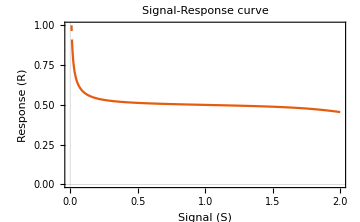

```mathematica
homeostasisSignalResponse
```

We see that... The response values are confined to a narrow window. This is because the homeostasis, or negative feedback loop, is self-regulating: if S gets higher, the rate goes up and thus th
Next, we plot the same graphs for Mutual Inhibition.

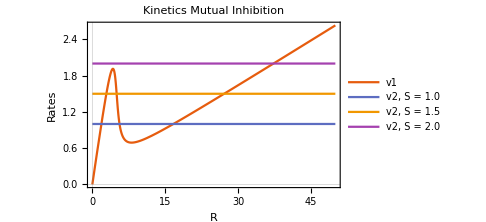

```mathematica
Remove[v1, v2, k0,k1,k2,k3,k4,J3,J4,s,r]

paramsInhibition={k0->0,k1->1,k2->0.05,k2b->0.5,k3->1,k4->0.2,J3->0.05,J4->0.05};
equationsB={v1-> k2*r+k2b*G[k3,k4*r,J3,J4]*r, v2->k0+k1*s};

mutualKinetics = Plot[{v1/.equationsB/.paramsInhibition, v2/.equationsB/.paramsInhibition/.s->1,v2/.equationsB/.paramsInhibition/.s->1.5,v2/.equationsB/.paramsInhibition/.s->2.0},{r,0,50},PlotTheme->"Scientific", 
PlotLabel-> Style["Kinetics Mutual Inhibition", FontSize-> 18],
Frame->True,
FrameLabel->{"R","Rates"}, 
PlotLegends->{"v1","v2, S = 1.0", "v2, S = 1.5","v2, S = 2.0"},
ImageSize-> Medium]

solInhibition = Solve[(v2 == v1) /. equationsB/.paramsInhibition,r];
signalResponseMutual = Plot[{r/.solInhibition⟦1⟧/.paramsInhibition, r/.solInhibition⟦2⟧/.paramsInhibition, r/.solInhibition⟦3⟧/.paramsInhibition},{s,0,2},
Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"Scientific",
PlotStyle->{{Orange, Dashed}, Orange, Orange} ,
PlotRange->{{0, 2},{0,30}},
Epilog->{Dashed, Gray, Line[{{{1.9, 0}, {1.9, 30}}, {{0.7,0},{0.7,30}}}]},
ImageSize->Medium];
```

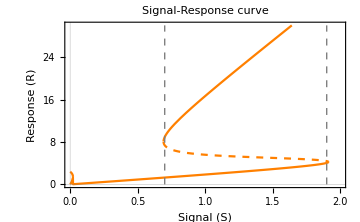

```mathematica
signalResponseMutual
```

The two vertical lines are the critical points. Part of the response curve is dashed: this is because this response strength can never exist. When the signal is lowered, the response will follow the

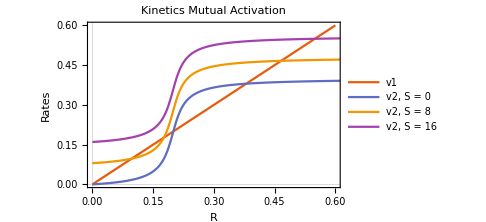

```mathematica
Remove[v1,v2,k0,k1,k2,k3,k4,J3,J4,s,r];

paramsActivation={k0->0.4,k1->0.01,k2->1,k3->1,k4->0.2,J3->0.05,J4->0.05};
equationsC={v2->k0*G[k3*r,k4,J3,J4]+k1*s,v1->k2*r};

kineticsActivation = Plot[{v1/.equationsC/.paramsActivation,v2/.equationsC/.paramsActivation/.s->0,v2/.equationsC/.paramsActivation/.s->8,v2/.equationsC/.paramsActivation/.s->16},{r,0,1},PlotRange->{{0,0.6},{0,0.6}},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"R","Rates"},
PlotLabel-> Style["Kinetics Mutual Activation", FontSize-> 18],
PlotLegends->{"v1","v2, S = 0", "v2, S = 8","v2, S = 16"},
ImageSize-> Medium]

solActivation=Solve[(v1== v2)/.equationsC/.paramsActivation,r];ResponseCurveActivation = Plot[{r/.solActivation⟦1⟧/.paramsActivation, r/.solActivation⟦2⟧/.paramsActivation, r/.solActivation⟦3⟧/.paramsActivation},{s,0,50},Frame->True,FrameLabel->{"Signal (S)","Response (R)"},PlotLabel->Style["Signal-Response curve",FontSize->18],PlotTheme->"Scientific", 
PlotRange->{{0, 15}, {0, 0.6}},
PlotStyle-> {{Orange, Dashed},Orange,Orange},
Epilog->{Dashed, Gray, Line[{{10.1, 0}, {10.1, 0.6}}]},
ImageSize->Medium];
```

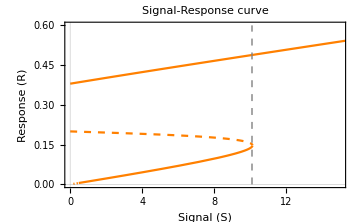

```mathematica
ResponseCurveActivation
```

Conclusions
In a feed-forward system, we see that the signal influences the response via two pathways. These push the response in opposite directions.

After studying these networks, we can conclude that figure 1b contains a model of positive feedback with mutual activation, figure 1c is positive feedback with mutual inhibition, and figure 1d is negative feedback or homeostasis. In figure 1d we see the negative feedback: the response R counteracts the effect of the stimulus S. In both 1b and 1c S enhances R, but in 2b R enhances also its own synthesis by phosphorylating E. This is called mutual activation. In 1c we see that R inhibits its own synthesis by phosphorylating E, and that is called mutual inhibition.

## Case study: The Lac operon - A switch

An operon is a part of the DNA containing a cluster of genes controlled by a promotor. In this section of this study, we take a closer look at the Lac-operon of Escherichia Coli, which has a promotor that is repressed by a repressor in the absence of lactose. When lactose is available in the medium, lactose is imported and converted into allolactose. Allolactose is at his turn able to inhibite the inhibitor of the promotor, and thereby allows the RNA polymerase to bind the promotor; mRNA is subsequently produced. 

-Graphics-
Figure 2: Schematic of the lac operon. The top scheme (a) shows the active repressor binding the operator in the absence of (allo)lactose, therefore inhibiting the transcription of the lac genes. Bottom scheme (b) shows deactivation of the repressor by allolactose, thereby deblocking the operator opening the way for the transcription of the lac genes.    


It is assumed that the production of mRNA is proportional to its translation into the proteins, and we can thus write the following system of ODEs as discussed in De Boer:
	ⅆM/ⅆt=k_1+k_2(1-1/(1 + A^n))-k_3 M
ⅆA/ⅆt=k_4 M L-k_5 A-V_max(M A)/(K_m + A)


Stability Analysis
ee that R inhibits its own synthesis by phosphorylating E, and that is calle

Results and Discussion
ee that R inhibits its own synthesis by phosphorylating E, and that is calle

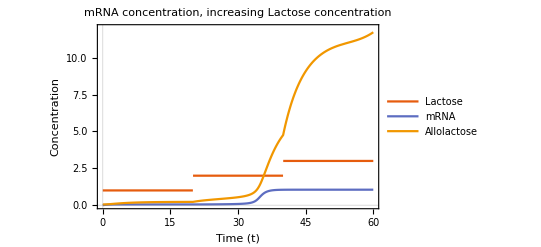

```mathematica
ClearAll["Global`*"]

k1 = 0.05;
k2 =  1;
k3 =  1;
L = 1;
Vmax =  1;
k4 =  1;
k5 = 0.2;
Km= 2;
n=5;

solved[t_] = NDSolve[{M'[t]== k1 + k2*(1- 1/(1+A[t]^n))-k3*M[t], A'[t]== k4*M[t]* (Floor[t/20]+1) - k5*A[t]-Vmax*M[t]*A[t]/(Km+A[t]), M[0]==0, A[0]==0.05}, {M[t],A[t]}, {t, 0 ,50}];

Plot[{Floor[t/20] + 1,M[t]/.solved[t], A[t]/.solved[t]}, {t,0,60}, PlotLegends-> {"Lactose", "mRNA", "Allolactose"}, 
PlotTheme->"Scientific",
Frame-> True,
FrameLabel->{"Time (t)", "Concentration"},
PlotLabel-> Style["mRNA concentration,\n increasing Lactose concentration", FontSize-> 18],
PlotRange->{{0,60},{0,12}}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

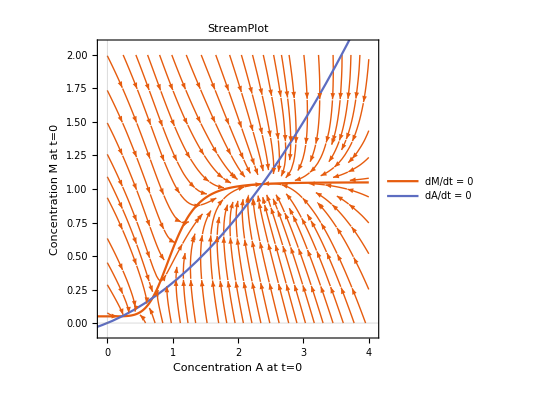

```mathematica
dM[A_, M_] = k1 + k2*(1- 1/(1+A^n))-k3*M;
dA[A_, M_] = k4*M* L - k5*A-Vmax*M*A/(Km+A);

streamplot = StreamPlot[{dA[A, M], dM[A, M]}, {A, 0, 4}, {M, 0, 2}, PlotLabel->"StreamPlot", FrameLabel-> {"Concentration A at t=0", "Concentration M at t=0"}, PlotTheme->"Scientific"];

f1 = M/.Solve[dM[A, M] == 0];
f2 = M/.Solve[dA[A, M] == 0];
isoclines = Plot[{f1, f2}, {A, -4, 4}, PlotLegends-> {"dM/dt = 0","dA/dt = 0"}, PlotTheme->"Scientific"];

Show[streamplot, isoclines]
```

Conclusions
dingen concluderen

## Simple Boolean network Qualitative chemical kinetic models